# Progetto Fondamenti di Automatica - Mariaida Perri mat. 239943 Esercizio b: Sistema LTI-TD

```mathematica
ClearAll["Global`*"]
```

Innanzitutto, inseriamo la terna di matrici A, B, C1 (il carattere C è riservato in Mathematica)

```mathematica
A= {{89/48,-49/24,-1/48},{1,-1,0},{137/48,-97/24,-1/48}}
```

{{89/48,-49/24,-1/48},{1,-1,0},{137/48,-97/24,-1/48}}

```mathematica
A//MatrixForm
```

(89/48 | -49/24 | -1/48
1 | -1 | 0
137/48 | -97/24 | -1/48)

```mathematica
B={{-1},{0},{-1}}
```

{{-1},{0},{-1}}

```mathematica
B//MatrixForm
```

(-1
0
-1)

```mathematica
C1 = {{2,2,-2}}
```

{{2,2,-2}}

```mathematica
C1//MatrixForm
```

(2 | 2 | -2)

1. Modi naturali del sistema

Calcoliamo lo spettro di A

```mathematica
p[λ_]:=CharacteristicPolynomial[A,λ]
```

```mathematica
p[λ]
```

1/48-(11 λ)/48+(5 λ^2)/6-λ^3

```mathematica
Solve[p[λ]==0,λ]
```

{{λ→1/4},{λ→1/4},{λ→1/3}}

```mathematica
Eigenvalues[A]
```

{1/3,1/4,1/4}

Controlliamo la molteplicità geometrica, per capire se la matrice è diagonalizzabile oppure no

```mathematica
NullSpace[A-(1/4)IdentityMatrix[3]]
```

{{-5/7,-4/7,1}}

Calcoliamo anche il polinomio minimo

```mathematica
MatrixMinimalPolynomial[a_List?MatrixQ,x_]:=Module[{i,n=1,qu={},mnm={Flatten[IdentityMatrix[Length[a]]]}},While[Length[qu]==0,AppendTo[mnm,Flatten[MatrixPower[a,n]]];
qu=NullSpace[Transpose[mnm]];
n++];
First[qu].Table[x^i,{i,0,n-1}]]
```

```mathematica
Factor[MatrixMinimalPolynomial[A,λ]]
```

1/48 (-1+3 λ) (-1+4 λ)^2

```mathematica
Factor[p[λ]]
```

-1/48 (-1+3 λ) (-1+4 λ)^2

Concludiamo che la matrice non è diagonalizzabile

Calcolo T e Λ

```mathematica
{T,Λ}=JordanDecomposition[A]
```

{{{-5/7,-368/49,-2},{-4/7,-272/49,-3/2},{1,0,1}},{{1/4,1,0},{0,1/4,0},{0,0,1/3}}}

```mathematica
T//MatrixForm
```

(-5/7 | -368/49 | -2
-4/7 | -272/49 | -3/2
1 | 0 | 1)

```mathematica
Λ//MatrixForm
```

(1/4 | 1 | 0
0 | 1/4 | 0
0 | 0 | 1/3)

```mathematica
Λp = MatrixPower[Λ,k]//MatrixForm
```

(4^-k | 4^(1-k) k | 0
0 | 4^-k | 0
0 | 0 | 3^-k)

Visualizziamo i grafici

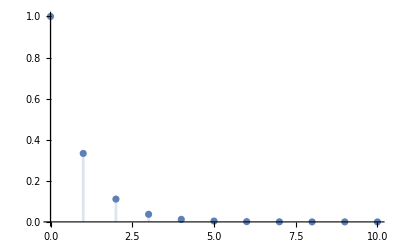

```mathematica
DiscretePlot[(1/3)^k,{k,0,10},PlotRange->All]
```

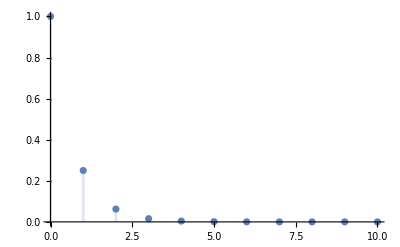

```mathematica
DiscretePlot[(1/4)^k,{k,0,10},PlotRange->All]
```

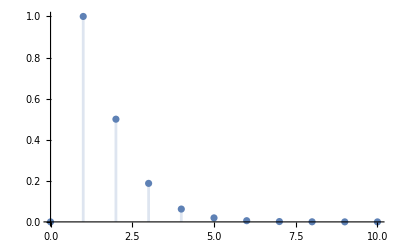

```mathematica
DiscretePlot[Binomial[k,1](1/4)^(k-1),{k,0,10},PlotRange->All]
```

```mathematica
Λ//MatrixForm
```

(1/4 | 1 | 0
0 | 1/4 | 0
0 | 0 | 1/3)

```mathematica
T//MatrixForm
```

(-5/7 | -368/49 | -2
-4/7 | -272/49 | -3/2
1 | 0 | 1)

```mathematica
Transpose[Eigenvectors[A]]//MatrixForm
```

(-2 | -5/7 | 0
-3/2 | -4/7 | 0
1 | 1 | 0)

La prima e la terza colonna di T rappresentano autovettori standard di A. Verifichiamo:

```mathematica
(A-(1/4)IdentityMatrix[3]).T[[All,1]]
```

{0,0,0}

```mathematica
(A-(1/3)IdentityMatrix[3]).T[[All,3]]
```

{0,0,0}

La seconda colonna è invece un autovettore generalizzato.

```mathematica
T[[All,1]]
```

{-5/7,-4/7,1}

```mathematica
(A-(1/4)IdentityMatrix[3]).T[[All,2]]
```

{-5/7,-4/7,1}

```mathematica
(A-(1/4)IdentityMatrix[3]).(A-(1/4)IdentityMatrix[3]).T[[All,2]]
```

{0,0,0}

2. Risposta libera dato lo stato iniziale x0

```mathematica
x0 = {{2},{1},{3}}
```

{{2},{1},{3}}

```mathematica
x0//MatrixForm
```

(2
1
3)

```mathematica
z0=Inverse[T].x0
```

{{19},{35/16},{-16}}

```mathematica
z0//MatrixForm
```

(19
35/16
-16)

Risposta libera nello stato

```mathematica
Subscript[x, l][k_]:=Simplify[T.MatrixPower[Λ,k].z0]
```

```mathematica
Subscript[x, l][k]//MatrixForm
```

(-15 2^(1-2 k)+32 3^-k-25 2^(-2 (1+k)) k
8 3^(1-k)-23 4^-k-5 4^-k k
-16 3^-k+19 4^-k+35 4^(-1-k) k)

Grafico

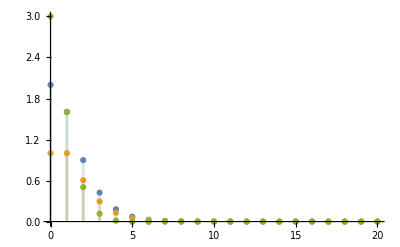

```mathematica
DiscretePlot[{{-15 2^(1-2 k)+32 3^-k-25 2^(-2 (1+k)) k},{8 3^(1-k)-23 4^-k-5 4^-k k},{-16 3^-k+19 4^-k+35 4^(-1-k) k}},{k,0,20},PlotRange->All]
```

Risposta libera nell'uscita

```mathematica
Subscript[y, l][k_]:=Simplify[C1.Subscript[x, l][k]]
```

```mathematica
Subscript[y, l][k]//MatrixForm
```

(8 (-9 2^(1-2 k)+2 3^(2-k)-5 2^(-2 k) k))

Grafico

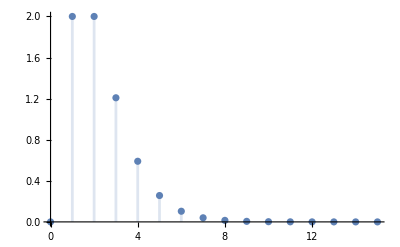

```mathematica
DiscretePlot[{8 (-9 2^(1-2 k)+2 3^(2-k)-5 2^(-2 k) k)},{k,0,15},PlotRange->All]
```

3. Studio della configurazione degli stati iniziali che attivano sulla risposta libera alcuni modi naturali ed altri no

Riprendiamo le matrici T e Λ

```mathematica
T//MatrixForm
```

(-5/7 | -368/49 | -2
-4/7 | -272/49 | -3/2
1 | 0 | 1)

```mathematica
Λ//MatrixForm
```

(1/4 | 1 | 0
0 | 1/4 | 0
0 | 0 | 1/3)

```mathematica
MatrixPower[Λ,k]//MatrixForm
```

(4^-k | 4^(1-k) k | 0
0 | 4^-k | 0
0 | 0 | 3^-k)

Stato iniziale allineato lungo la prima colonna di T

```mathematica
x0 = T[[All,1]]
```

{-5/7,-4/7,1}

```mathematica
z0=Inverse[T].x0
```

{1,0,0}

```mathematica
Subscript[x, l][k_]:=Simplify[T.MatrixPower[Λ,k].z0]
```

```mathematica
Subscript[x, l][k]//MatrixForm
```

(-(5 4^-k)/7
-4^(1-k)/7
4^-k)

Stato iniziale allineato lungo la seconda colonna di T

```mathematica
x0=T[[All,2]]
```

{-368/49,-272/49,0}

```mathematica
z0=Inverse[T].x0
```

{0,1,0}

```mathematica
Subscript[x, l][k_]:=Simplify[T.MatrixPower[Λ,k].z0]
```

```mathematica
Subscript[x, l][k]//MatrixForm
```

(-1/49 4^(1-k) (92+35 k)
-1/49 4^(2-k) (17+7 k)
4^(1-k) k)

Stato iniziale allineato lungo la terza colonna di T

```mathematica
x0 = T[[All,3]]
```

{-2,-3/2,1}

```mathematica
z0=Inverse[T].x0
```

{0,0,1}

```mathematica
Subscript[x, l][k_]:=Simplify[T.MatrixPower[Λ,k].z0]
```

```mathematica
Subscript[x, l][k]//MatrixForm
```

(-2 3^-k
-3^(1-k)/2
3^-k)

Stato iniziale allineato ad una combinazione lineare della prima e terza colonna di T

```mathematica
x0=T[[All,1]]+T[[All,3]]
```

{-19/7,-29/14,2}

```mathematica
z0 = Inverse[T].x0
```

{1,0,1}

```mathematica
Subscript[x, l][k_]:=Simplify[T.MatrixPower[Λ,k].z0]
```

```mathematica
Subscript[x, l][k]//MatrixForm
```

(-2 3^-k-(5 4^-k)/7
-3^(1-k)/2-4^(1-k)/7
3^-k+4^-k)

4. Funzione di trasferimento, i suoi poli e zeri

Calcoliamo la FdT

```mathematica
G[z_]:=Simplify[C1.Inverse[z IdentityMatrix[3]-A].B]
```

```mathematica
G[z]
```

{{-96/((1-4 z)^2 (-1+3 z))}}

```mathematica
CharacteristicPolynomial[A,z]
```

1/48-(11 z)/48+(5 z^2)/6-z^3

Poli

```mathematica
Solve[Denominator[G[z]]==0,z]
```

{{z→1/4},{z→1/4},{z→1/3}}

Zeri

```mathematica
Solve[Numerator[G[z]]==0,z]
```

{}

Verifichiamo, incapsulando le matrici A, B e C1 in una struttura StateSpaceModel

```mathematica
Σ = StateSpaceModel[{A,B,C1}]
```

89/48-49/24-1/48-11-100137/48-97/24-1/48-122-20StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionModel[Σ]
```

2/(1/48-(11 s)/48+(5 s^2)/6-s^3)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11211FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionPoles[Σ]
```

{{{1/4,1/4,1/3}}}

```mathematica
TransferFunctionZeros[Σ]
```

{{{}}}

5. Risposta al gradino unitario e suo grafico

Calcoliamo la risposta forzata

```mathematica
Subscript[Y, f][z_]:=G[z](z/(z-1))
```

```mathematica
Subscript[Y, f][z]
```

{{-(96 z)/((1-4 z)^2 (-1+z) (-1+3 z))}}

Dividiamo Y_f[z] per z

```mathematica
(Subscript[Y, f][z])/z
```

{{-96/((1-4 z)^2 (-1+z) (-1+3 z))}}

Determiniamo i fratti semplici

```mathematica
Expand[Apart[-96/((1-4 z)^2 (-1+z) (-1+3 z))]]
```

-16/(3 (-1+z))+1296/(-1+3 z)-512/(-1+4 z)^2-5120/(3 (-1+4 z))

Otteniamo 4 fratti semplici, tanti quanti il grado del denominatore

```mathematica
Subscript[C, 1]/(z-1)+Subscript[C, 22]/(z-1/4)^2+Subscript[C, 21]/(z-1/4)+Subscript[C, 3]/(z-1/3)
```

C_1/(-1+z)+C_3/(-1/3+z)+C_21/(-1/4+z)+C_22/(-1/4+z)^2

Tramite la formula di Heaviside generalizzata determiniamo i coefficienti C

```mathematica
Subscript[C, 1]=lim_(z->1) (z-1)((Subscript[Y, f][z])/z)[[1,1]]
```

-16/3

```mathematica
Subscript[C, 1]=G[1]
```

{{-16/3}}

```mathematica
Subscript[C, 22]=lim_(z->1/4) (z-1/4)^2((Subscript[Y, f][z])/z)[[1,1]]
```

-32

```mathematica
Subscript[C, 21]=lim_(z->1/4) D[(z-1/4)^2((Subscript[Y, f][z])/z),z][[1,1]]
```

-1280/3

```mathematica
Subscript[C, 3]=lim_(z->1/3) (z-1/3)((Subscript[Y, f][z])/z)[[1,1]]
```

432

```mathematica
Subscript[C, 1]/(z-1)+Subscript[C, 22]/(z-1/4)^2+Subscript[C, 21]/(z-1/4)+Subscript[C, 3]/(z-1/3)
```

{{-16/(3 (-1+z))+432/(-1/3+z)-32/(-1/4+z)^2-1280/(3 (-1/4+z))}}

Moltiplichiamo per z

```mathematica
Subscript[C, 1](z/(z-1))+Subscript[C, 22](z/(z-1/4)^2)+Subscript[C, 21](z/(z-1/4))+Subscript[C, 3](z/(z-1/3))
```

{{-(16 z)/(3 (-1+z))+(432 z)/(-1/3+z)-(32 z)/(-1/4+z)^2-(1280 z)/(3 (-1/4+z))}}

Dobbiamo ricondurci alla forma Z{α^k 1(k)}:=z/(z-α)

```mathematica
yf[k_]:=Subscript[C, 1] UnitStep[k]+Subscript[C, 22] k(1/4)^(k-1)UnitStep[k]+Subscript[C, 21](1/4)^k UnitStep[k]+Subscript[C, 3](1/3)^k UnitStep[k]
```

```mathematica
yf[k]
```

{{-(16 UnitStep[k])/3+16 3^(3-k) UnitStep[k]-5/3 4^(4-k) UnitStep[k]-2^(7-2 k) k UnitStep[k]}}

Controlliamo se il risultato è corretto

```mathematica
Expand[InverseZTransform[Subscript[Y, f][z],z,k]]
```

{{-16/3+16 3^(3-k)-(5 4^(4-k))/3-2^(7-2 k) k}}

Risposta a regime

```mathematica
yr[k_]:=Subscript[C, 1] UnitStep[k]
```

```mathematica
yr[k]
```

{{-(16 UnitStep[k])/3}}

Risposta transitoria

```mathematica
yt[k_]:=Subscript[C, 22] k(1/4)^(k-1)UnitStep[k]+Subscript[C, 21](1/4)^k UnitStep[k]+Subscript[C, 3](1/3)^k UnitStep[k]
```

```mathematica
yt[k]
```

16 3^(3-k) UnitStep[k]-5/3 4^(4-k) UnitStep[k]-2^(7-2 k) k UnitStep[k]

Controlliamo che la risposta transitoria, combinazione lineare dei modi naturali, converga a zero quando k -> ∞ .

```mathematica
lim_(k->+∞) 432(1/3)^k-1280/3(1/4)^k-32k(1/4)^(k-1)
```

0

Grafico della risposta al gradino

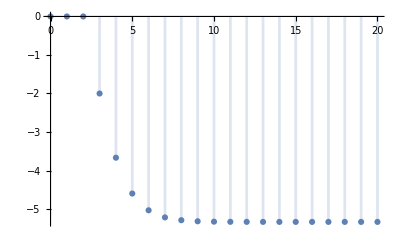

```mathematica
DiscretePlot[{-(16 UnitStep[k])/3+16 3^(3-k) UnitStep[k]-5/3 4^(4-k) UnitStep[k]-2^(7-2 k) k UnitStep[k]},{k,0,20},PlotRange->All]
```

Grafico delle risposte al sistema

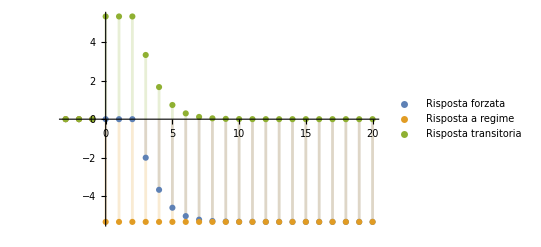

```mathematica
DiscretePlot[{-(16 UnitStep[k])/3+16 3^(3-k) UnitStep[k]-5/3 4^(4-k) UnitStep[k]-2^(7-2 k) k UnitStep[k],-(16 UnitStep[k])/3,16 3^(3-k) UnitStep[k]-5/3 4^(4-k) UnitStep[k]-2^(7-2 k) k UnitStep[k]},{k,-3,20},PlotRange->All,PlotLegends->{"Risposta forzata","Risposta a regime","Risposta transitoria"}]
```

Una volta esaurito il transitorio, la risposta forzata si assesta sul valore costante relativo alla risposta a regime (-16/3).

6. Modelli ARMA equivalenti

```mathematica
G[z][[1,1]]
```

-96/((1-4 z)^2 (-1+3 z))

Inseriamo l'equazione alle differenze

```mathematica
ed = -y[k]+11y[k+1]-40y[k+2]+48y[k+3]==-96u[k]
```

-y[k]+11 y[1+k]-40 y[2+k]+48 y[3+k]==-96 u[k]

```mathematica
ZTransform[ed,k,z]
```

-ZTransform[y[k],k,z]+11 (-z y[0]+z ZTransform[y[k],k,z])-40 (-z^2 y[0]-z y[1]+z^2 ZTransform[y[k],k,z])+48 (-z^3 y[0]-z^2 y[1]-z y[2]+z^3 ZTransform[y[k],k,z])==-96 ZTransform[u[k],k,z]

-Y[z]+11(-zy[0]+zY[z])-40(-z^2y[0]-zy[1]+z^2 Y[z])+48(-z^3y[0]-z^2 y[1]-zy[2]+z^3 Y[z])==-96U[z]

Consideriamo le seguenti condizioni iniziali

```mathematica
x0 = {{3},{1},{3}}
```

{{3},{1},{3}}

```mathematica
x0//MatrixForm
```

(3
1
3)

```mathematica
C1
```

{{2,2,-2}}

```mathematica
y[0]=(C1.x0)[[1,1]]
```

2

```mathematica
y[1]=(C1.A.x0)[[1,1]]
```

2

```mathematica
y[2]=(C1.A.A.x0)[[1,1]]
```

4

Sostituiamo:

```mathematica
espr =-Y[z]+11(-z y[0]+z  Y[z])-40(-z^2 y[0]-z y[1]+z^2 Y[z])+48(-z^3 y[0]-z^2 y[1]-z y[2]+z^3 Y[z])==-96U[z]
```

-Y[z]+11 (-2 z+z Y[z])-40 (-2 z-2 z^2+z^2 Y[z])+48 (-4 z-2 z^2-2 z^3+z^3 Y[z])==-96 U[z]

```mathematica
Solve[espr,Y[z]][[1,1]]
```

Y[z]→(2 (67 z+8 z^2+48 z^3-48 U[z]))/((-1+3 z) (-1+4 z)^2)

Dopo aver posto U[z] = 1, calcoliamo l'antitrasformata Z della FdT, ottenendo la risposta all'impulso

```mathematica
g[k_]:=InverseZTransform[(2 (67 z+8 z^2+48 z^3-48 ))/((-1+3 z) (-1+4 z)^2),z,k]
```

```mathematica
g[k]
```

-2^(1-2 k) 3^-k (207 2^(2 k)-160 3^k-40 3^(1+k) k) (1-UnitStep[-k])+2 UnitStep[-k]

Ne visualizziamo il grafico

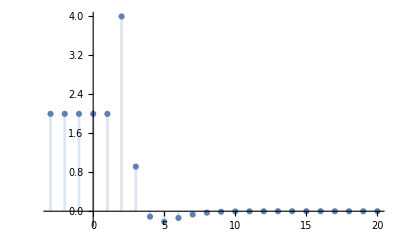

```mathematica
DiscretePlot[g[k],{k,-3,20},PlotRange->All]
```

Risposta all'ingresso assegnato u(k)

```mathematica
u[k_]:=Piecewise[{{1,0<=k<=10}},0]
```

```mathematica
u[k]
```

Piecewise[{{1, 0≤k≤10}, {0, True}}]

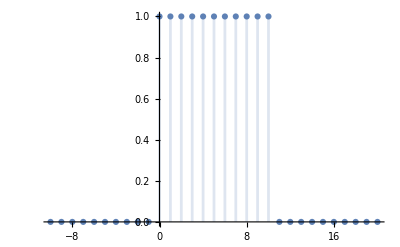

```mathematica
DiscretePlot[u[k],{k,-10,20},PlotRange->All]
```

Calcoliamo la risposta al segnale tramite una somma di convoluzione

```mathematica
Subscript[y, f][k_]:= ∑_(n=0)^k g[k]×u[k-n]
```

```mathematica
Subscript[y, f][k]
```

Piecewise[{{2, k==0}, {-11 2^(1-2 k) 3^-k (207 2^(2 k)-160 3^k-40 3^(1+k) k), k>10}, {-2^(1-2 k) 3^-k (1+k) (207 2^(2 k)-160 3^k-40 3^(1+k) k), True}}]

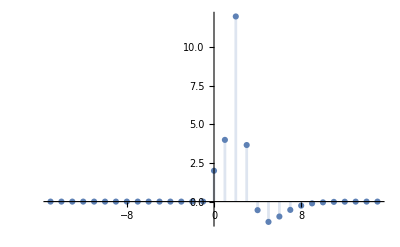

```mathematica
DiscretePlot[Subscript[y, f][k],{k,-15,15},PlotRange->All]
```

7. Condizioni iniziali tali che la risposta al gradino coincida con il suo valore di regime

```mathematica
x0={{x1},{x2},{x3}}
```

{{x1},{x2},{x3}}

```mathematica
x0//MatrixForm
```

(x1
x2
x3)

A partire dal modello ARMA trovato al punto precedente, isoliamo la risposta forzata Y(z) e sostituiamo a U(z) la Z-Trasformata della risposta al gradino

```mathematica
Y[z]=(2 (67 z+8 z^2+48 z^3-48 U[z]))/((-1+3 z) (-1+4 z)^2)
```

(2 (67 z+8 z^2+48 z^3-48 U[z]))/((-1+3 z) (-1+4 z)^2)

```mathematica
U[z]=z/(z-1)
```

z/(-1+z)

```mathematica
Y[z]
```

(2 (67 z-(48 z)/(-1+z)+8 z^2+48 z^3))/((-1+3 z) (-1+4 z)^2)

Calcoliamo la risposta a regime, la risposta transitoria e la risposta libera

```mathematica
G[z]
```

{{-96/((1-4 z)^2 (-1+3 z))}}

```mathematica
regime = G[1]U[z]
```

{{-(16 z)/(3 (-1+z))}}

```mathematica
transitoria=Factor[Y[z]-regime][[1,1]]
```

(2 z (353+88 z+528 z^2))/(3 (-1+3 z) (-1+4 z)^2)

```mathematica
libera = Simplify[z C1.Inverse[z IdentityMatrix[3]-A].x0][[1,1]]
```

(2 z (x3 (-11+40 z-48 z^2)+x1 (59-40 z+48 z^2)+x2 (-77+8 z+48 z^2)))/((1-4 z)^2 (-1+3 z))

Per far sì che sia nulla, effettuiamo la somma tra risposta libera e risposta transitoria ed estraiamo il numeratore per eguagliarlo a 0

```mathematica
num = Numerator[Simplify[Expand[libera+transitoria]]]
```

2 z (353-33 x3+88 z+120 x3 z+528 z^2-144 x3 z^2+3 x1 (59-40 z+48 z^2)+3 x2 (-77+8 z+48 z^2))

```mathematica
cf = CoefficientList[num,z]
```

{0,706+354 x1-462 x2-66 x3,176-240 x1+48 x2+240 x3,1056+288 x1+288 x2-288 x3}

Eguagliamo a {0, 0, 0,0} i valori ottenuti ed otteniamo le componenti dello stato iniziale

```mathematica
Solve[cf=={0,0,0,0},{x1,x2,x3}]
```

{{x1→-25/3,x2→-11/3,x3→-25/3}}

```mathematica
x0={{-25/3},{-11/3},{-25/3}}//MatrixForm
```

(-25/3
-11/3
-25/3)

Verifichiamo con una struttura StateSpaceModel che, dato lo stato iniziale trovato, la risposta al gradino coincida con la risposta a regime:

```mathematica
check = StateSpaceModel[{A,B,C1},SamplingPeriod->1]
```

89/48-49/24-1/48-11-100137/48-97/24-1/48-122-201StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
FullSimplify[OutputResponse[{check,{-25/3,-11/3,-25/3}},1,k],k∈ Integers][[1,1]]
```

-16/3

```mathematica
rr=Expand[InverseZTransform[regime,z,k]][[1,1]]
```

-16/3

Lo stato iniziale trovato è corretto.